```mathematica
palette={ColorData["Pastel"][0],ColorData["Pastel"][0.3],ColorData["Pastel"][1],ColorData["Pastel"][0.8],ColorData["BrightBands"][0.1],ColorData["BrightBands"][0.]}
susyRatio2states=4/(9 π^2);
susyRatio=125/(858 π^2);
accuRatio=-22/3 (-31053+44800 Log[2]);
r0=5{1,GoldenRatio};
r1=5{15/20.5,GoldenRatio};
SpecialTextRotation[text_,{xPos_,yPos_},angle_,{xRange_,yRange_},ratio_:GoldenRatio]:=Module[{SRS},
SRS=({{xRange, 0}, {0, yRange ratio}}).RotationMatrix[angle].({{1/xRange, 0}, {0, 1/(yRange ratio)}});
GeometricTransformation[Text[text,{xPos,yPos}],{SRS,Flatten[(IdentityMatrix[2]-SRS).({{xPos}, {yPos}})]}]
]
star=Polygon[…];
```

{RGBColor[0.761959, 0.470832, 0.940597],RGBColor[0.9177137, 0.7189139, 0.632918],RGBColor[0.431296, 0.709773, 0.927077],RGBColor[0.7952328000000001, 0.8988539999999999, 0.8302508],RGBColor[0.966153150692097, 0.42917541619317257, 0.5595256860227147],RGBColor[0.90222, 0.101808, 0.198306]}

### 3 state, 0 sub, μ change

```mathematica
ClearAll[points,spectrum]
points[6.5]=;
points[7.]=;
points[7.5]=;
points[6.]=[[1]];
points[7.]=[[2]];
points[8.]=;
spectrum[6.5]=;
spectrum[7.]=;
spectrum[7.5]=;
```

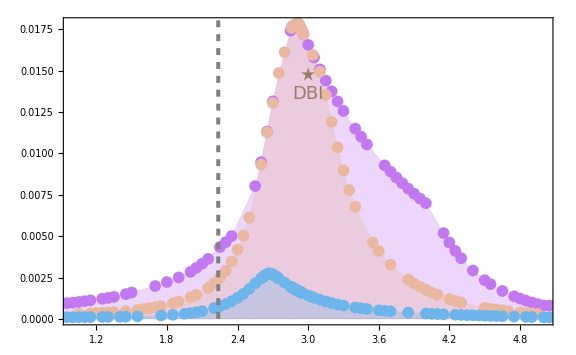

```mathematica
ListLinePlot[Evaluate[points/@{6.,7.,8.}],PlotTheme->"Scientific",PlotMarkers->{"●", 12},PlotStyle->Evaluate[{Thickness[0.00],#}&/@palette],ImageSize->Large,FrameLabel->Evaluate[Style[#,25,FontFamily->"Times New Roman [TMC ]"]&/@{"",""}],FrameTicksStyle->Directive[18,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{1,
5},{0,All}}];
Graphics[{
Darker@palette[[2]],
GeometricTransformation[star,Composition[TranslationTransform[{3,susyRatio}],ScalingTransform[0.015{4,0.018GoldenRatio}]]],
Text[Style["DBI",18],{3.,susyRatio-0.0012}],
Gray,Dashed,Thickness[0.005],
Line[{{√5,0},{1,200}}],
Darker@palette[[1]],
SpecialTextRotation[Style["",18],{3.7,0.0105},-0.8,{4,0.018}],
Darker@palette[[2]],
SpecialTextRotation[Style["",18],{3.9,0.0035},-0.6,{4,0.018}],
Darker@palette[[3]],
SpecialTextRotation[Style["",18],{3.5,0.0015},-0.1,{4,0.018}]
}];
Show[%%,%]
```

```mathematica
Export[NotebookDirectory[]<>"/Figures/3state_0sub_muChange.pdf",]
```

~/Physics/Gapped Bootstrap/Figures/3state_0sub_muChange.pdf

```mathematica
ClearAll[spectrum]
spectrum[2.92]=;
spectrum[3.15]=;
spectrum[3.75]=;
spectrum[4.]=;
```

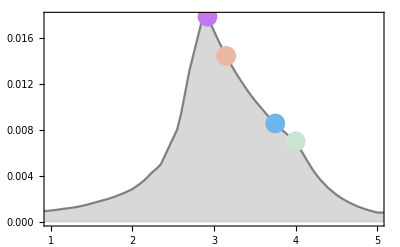

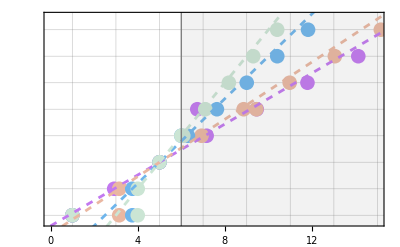

```mathematica
ListLinePlot[points[6.],PlotTheme->"Scientific",PlotStyle->Gray,ImageSize->{Automatic,360},FrameLabel->Evaluate[Style[#,25,FontFamily->"Times New Roman [TMC ]"]&/@{"",""}],FrameTicks->{{All, None}, {All, None}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{1,
5},{0,All}}];
ListPlot[{#}&/@,PlotMarkers->{"●", 20},PlotStyle->palette];
Show[%%,%]
ListPlot[Evaluate[({m2,l}/.DeleteCases[spectrum[#],_?(λ<10^-5/.#&)])&/@{2.92,3.15,3.75,4.}],PlotMarkers->{"●", 15},PlotStyle->palette,PlotTheme->"Scientific",PlotRange->{{0,15},{-0.5,15}},FrameLabel->Evaluate[{{None,Style["",30,FontFamily->"Times New Roman [TMC ]"]},{Style["",25,FontFamily->"Times New Roman [TMC ]"],None}}],FrameTicks->{{None, All}, {All, None}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],ImageSize->{Automatic,360},GridLines->{Range[1,20,2],Range[0,20,2]}];
Plot[Evaluate[(2/(5-#)(m2-5)+4)&/@{2.92,3.15,3.75,4.}],{m2,0,20},PlotStyle->Evaluate[{Dashed,#}&/@palette]];
Graphics[{
Gray,Thin,
Line[{{6,-1},{6,20}}],
Opacity[0.1],
Rectangle[{6,-1},{20,20}]
}];
Show[%%%,%%,%]
```

```mathematica
Grid[{{,,SpanFromLeft}},Alignment->Bottom,Spacings->{3,0}]
```

-Graphics- | -Graphics- |

```mathematica
Export[NotebookDirectory[]<>"/Figures/ski_slopes.pdf",]
```

~/Physics/Gapped Bootstrap/Figures/ski_slopes.pdf

### 3 states, 0 subs, shifted

```mathematica
ClearAll[points,spectrum]
points[0.]=;
points[0.5]=;
points[1.]=;
points[-0.2]=;
spectrum[0.]=;
spectrum[0.5]=;
spectrum[1.]=;
spectrum[-0.2]=;
```

```mathematica
pointsModified[muShift_]:={1/(1+muShift)#[[1]],#[[2]]}&/@points[muShift]
```

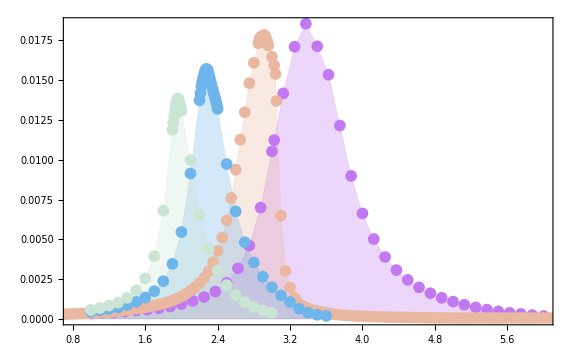

```mathematica
ListLinePlot[Evaluate[pointsModified/@{-0.2,0.,0.5,1.}],PlotTheme->"Scientific",PlotMarkers->{"●", 12},PlotStyle->Evaluate[{Thickness[0.00],#}&/@palette],ImageSize->Large,FrameLabel->Evaluate[Style[#,25,FontFamily->"Times New Roman [TMC ]"]&/@{"",""}],FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{0.8,
6},{0,All}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"]];
Graphics[{
Darker@palette[[1]],
SpecialTextRotation[Style["",18],{3.2,0.011},1.34,{6-0.8,0.0188}],
Darker@palette[[2]],
SpecialTextRotation[Style["",18],{2.8,0.011},1.4,{6-0.8,0.0188}],
Darker@palette[[3]],
SpecialTextRotation[Style["",18],{2.22,0.0075},1.4,{6-0.8,0.0188}],
Darker@palette[[4]],
SpecialTextRotation[Style["",18],{1.65,0.0075},1.44,{6-0.8,0.0188}]
}];
Show[%%,%]
```

```mathematica
Export[NotebookDirectory[]<>"/Figures/3state_0sub_shift.pdf",]
```

~/Physics/Gapped Bootstrap/Figures/3state_0sub_shift.pdf

### 2 states, 0 subs, m1 and μ change

```mathematica
ClearAll[points,spectrum]
points[M_]:=Join[M/.,M/.Append[,1.->{}],M/.]//SortBy[First]
spectrum[0.8]=;
spectrum[0.35]=;
spectrum[0.5]=;
spectrum[0.95]=;
spectrum[0.333]=;
spectrum[DBI]=Prepend[#[[2;;]],m2->(m2/.#)/3]&/@;
```

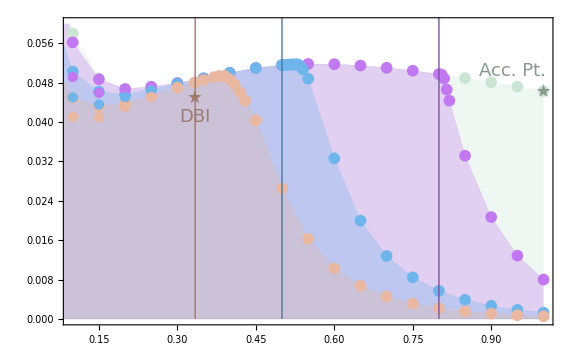

```mathematica
Graphics[{
Thin,
Darker@palette[[1]],
Line[{{2-1.2,0},{2-1.2,1}}],
Darker@palette[[3]],
Line[{{2-1.5,0},{2-1.5,1}}],
Darker@palette[[2]],
Line[{{2-1.666,0},{2-1.666,1}}]
}];
ListLinePlot[Evaluate[points/@{1.,1.2,1.5,1.66}],PlotTheme->"Scientific",PlotMarkers->{"●", 12},PlotStyle->Evaluate[{Thickness[0.00],#}&/@{palette[[4]],palette[[1]],palette[[3]],palette[[2]]}],ImageSize->Large,FrameLabel->Evaluate[Style[#,25,FontFamily->"Times New Roman [TMC ]"]&/@{"",""}],FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{0.1,
1},{0,0.06}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"]];
Graphics[{
Darker@palette[[2]],
GeometricTransformation[star,Composition[TranslationTransform[{1/3,susyRatio2states}],ScalingTransform[0.015{0.9,0.06GoldenRatio}]]],
Text[Style["DBI",18],{1/3,susyRatio2states-0.004}],
Darker@palette[[4]],
GeometricTransformation[star,Composition[TranslationTransform[{1,accuRatio}],ScalingTransform[0.015{0.9,0.06GoldenRatio}]]],
Text[Style["Acc. Pt.",18],{1-0.06,accuRatio+0.004}],
Darker@palette[[4]],
SpecialTextRotation[Style["",18],{0.9,0.045},-0.15,{0.9,0.06}],

Darker@palette[[1]],
SpecialTextRotation[Style["",18],{0.68,0.048},-0.07,{0.9,0.06}],
Darker@palette[[3]],
SpecialTextRotation[Style["",18],{0.57,0.034},-1.2,{0.9,0.06}],
Darker@palette[[2]],
SpecialTextRotation[Style["",18],{0.47,0.025},-1.14,{0.9,0.06}]
}];
ListPlot[{1.2,1.5,1.66}/.,PlotStyle->{palette[[1]],palette[[3]],palette[[2]]}];
Show[%%%,%%%%,%%,%]
```

```mathematica
palette2=ColorData["BrightBands"]/@{0.4,0.2,0.,1}
```

{RGBColor[0.35957884292551023, 0.8083001713070861, 1.],RGBColor[0.512227148190099, 0.42680966628910977, 0.9998892092475745],RGBColor[0.90222, 0.101808, 0.198306],RGBColor[1., 0.749752, 0.501183]}

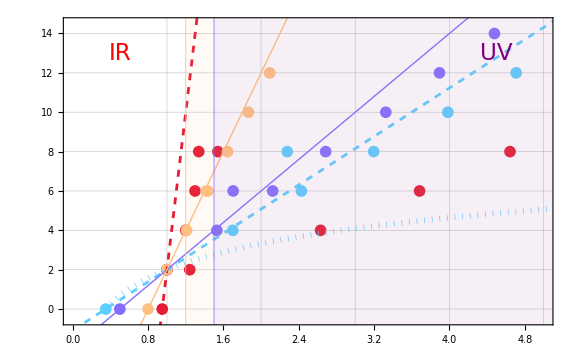

```mathematica
ListPlot[Evaluate[({m2,l}/.DeleteCases[spectrum[#],_?(λ<10^-5/.#&)])&/@{0.35,0.5,0.95,0.8}],PlotMarkers->{"●", 12},PlotStyle->palette2,PlotTheme->"Scientific",PlotRange->{{0,5},{-0.5,14.5}},FrameLabel->Evaluate[{Style["",25,FontFamily->"Times New Roman [TMC ]"],Style["",30,FontFamily->"Times New Roman [TMC ]"]}],FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],ImageSize->Large,GridLines->{Range[1,20,1],Range[0,20,2]}];
Plot[Evaluate[(2/(1-#)(m2-1)+2)&/@{0.35,0.5,0.95,0.8}],{m2,0,20},PlotStyle->Evaluate[{{Dashed,Thick,Dashed,Thick},palette2}ᵀ]];
Plot[Evaluate[2(1-Log[m2]/Log[#])&/@{0.35}],{m2,0,20},PlotStyle->Evaluate[{Dotted,#,Thickness[0.007]}&/@{palette2[[1]]}]];
Graphics[{
palette2[[4]],
Thickness[0.001],
Line[{{1.2,-30},{1.2,30}}],
Opacity[0.07],
Rectangle[{1.2,-30},{30,30}],
Opacity[1],
palette2[[2]],
Line[{{1.5,-30},{1.5,30}}],
Opacity[0.07],
Rectangle[{1.5,-30},{30,30}],
Opacity[1],
palette2[[4]],
SpecialTextRotation[Style["",18],{1.75,11.4},1.15,{5,15}],
palette2[[1]],
SpecialTextRotation[Style["",18],{4,9},.5,{5,15}],
palette2[[2]],
SpecialTextRotation[Style["",18],{3.,11},.72,{5,15}],
palette2[[3]],
SpecialTextRotation[Style["",18],{4.2,6},.4,{5,15}],
Red,
Text[Style["IR",23],{0.5,13}],
Purple,
Text[Style["UV",23],{4.5,13}]
}];
Show[%%%%,%%%,%%,%]
```

```mathematica
Export[NotebookDirectory[]<>"/Figures/2state0Sub2.pdf",]
```

~/Physics/Gapped Bootstrap/Figures/2state0Sub2.pdf

```mathematica
Export[NotebookDirectory[]<>"/Figures/2state0Sub2_spectra.pdf",]
```

~/Physics/Gapped Bootstrap/Figures/2state0Sub2_spectra.pdf

### 2 states, -2 subs, m1 and μ change

```mathematica
ClearAll[points,spectrum]
points[3.5]=;
points[3.3]=;
points[3.0]=;
points[2.8]=;
points[2.4]=;
points[2.0]=;
```

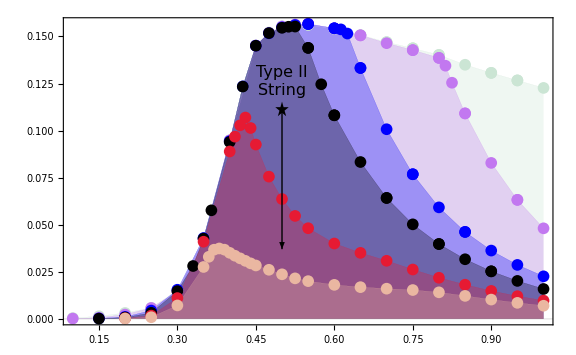

```mathematica
ListLinePlot[Evaluate[points/@{2.,2.4,2.8,3.,3.3,3.5}],PlotTheme->"Scientific",PlotMarkers->{"●", 12},PlotStyle->Evaluate[{Thickness[0.00],#}&/@{palette[[4]],palette[[1]],Blue,Black,palette[[6]],palette[[2]]}],ImageSize->Large,FrameLabel->Evaluate[Style[#,25,FontFamily->"Times New Roman [TMC ]"]&/@{"",""}],FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{0.1,
1},{0,All}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"]];
Graphics[{
Black,Arrowheads[.03],Thick,
GeometricTransformation[star,Composition[TranslationTransform[{1/2,1/9}],ScalingTransform[0.015{0.9,0.177GoldenRatio}]]],
Text[Style["Type II\nString",16],{1/2,1/9+0.015}],
Arrow[{{1/2,1/9},{1/2,1/27}}],
Darker@palette[[4]],
SpecialTextRotation[Style["",18],{0.92,0.12},-0.23,{0.9,0.177}],

Darker@palette[[1]],
SpecialTextRotation[Style["",18],{0.87,0.085},-0.95,{0.9,0.177}],
Darker@Blue,
SpecialTextRotation[Style["",18],{0.71,0.08},-0.95,{0.9,0.177}],
Black,
SpecialTextRotation[Style["",18],{0.65,0.07},-0.85,{0.9,0.177}],
Darker@palette[[6]],
SpecialTextRotation[Style["",18],{0.63,0.03},-0.32,{0.9,0.177}],
palette[[2]],
SpecialTextRotation[Style["",18],{0.55,0.012},-0.1,{0.9,0.177}]
}];
Show[%%,%]
```

```mathematica
Export[NotebookDirectory[]<>"/Figures/2_grav_traj_sara.pdf",]
```

~/Physics/Gapped Bootstrap/Figures/2_grav_traj_sara.pdf

### NC convergence

```mathematica
ClearAll[points,spectrum]
points[8]=[[1]];
points[10]=[[2]];
points[12]=[[3]];
points[14]=;
points[16]=[[4]];
points[18]=[[1]];
points[20]=[[2]];
```

```mathematica
palette3=ColorData["Rainbow"]/@{0,0.25,0.5,0.75,1}
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

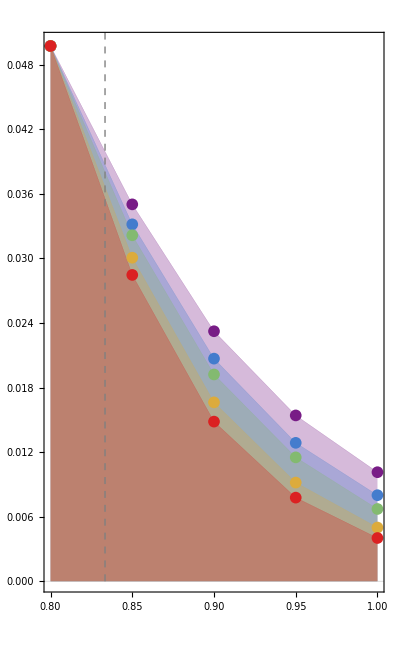

```mathematica
ListLinePlot[Evaluate[points/@{12,14,16,18,20}],PlotTheme->"Scientific",PlotMarkers->{"●", 12},PlotStyle->Evaluate[{Thickness[0.00],#}&/@palette3],ImageSize->{Automatic,500},FrameLabel->Evaluate[Style[#,25,FontFamily->"Times New Roman [TMC ]"]&/@{"",""}],FrameTicks->{{All, None}, {All, None}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{0.8,
1},{0,0.05}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],AspectRatio->GoldenRatio,PlotLegends->Placed[Style[#,18,FontFamily->"Times New Roman [TMC ]"]&/@{"","","","",""},1/GoldenRatio{1.2,1}]];
Graphics[{
Gray, Thick, Dashed,
Line[{{5/6,0},{5/6,200}}]
}];
Show[%%,%]
```

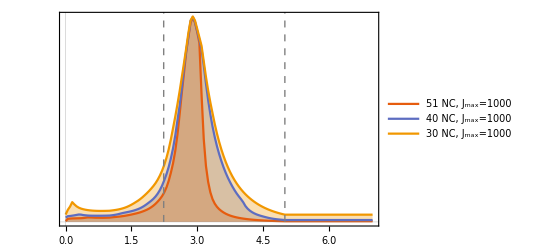

```mathematica
ListLinePlot[{,,},PlotTheme->"Scientific",ImageSize->{Automatic,500},FrameLabel->Evaluate[{{None,""//Style[#,25,FontFamily->"Times New Roman [TMC ]"]&},{""//Style[#,25,FontFamily->"Times New Roman [TMC ]"]&,None}}],FrameTicks->{{None, All}, {All, None}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{0,7},{0,All}},PlotLegends->Placed[Style[#,18,FontFamily->"Times New Roman [TMC ]"]&/@{"51 NC, J_max=1000","40 NC, J_max=1000", "30 NC, J_max=1000"},{0.85,0.6}]];
Graphics[{
Gray, Thick, Dashed,
Line[{{√5,0},{1,200}}],
Line[{{5,0},{1,200}}]
}];
Show[%%,%]
```

```mathematica
Grid[{{,,SpanFromLeft}},Alignment->Bottom,Spacings->{3,0}]
```

-Graphics- | -Graphics- |

```mathematica
Export[NotebookDirectory[]<>"/Figures/NCconvergence.pdf",]
```

~/Physics/Gapped Bootstrap/Figures/NCconvergence.pdf

### 3 states, -2 subs

```mathematica
ClearAll[points];points[3.5]=;points[4.0]=;points[4.5]=;
```

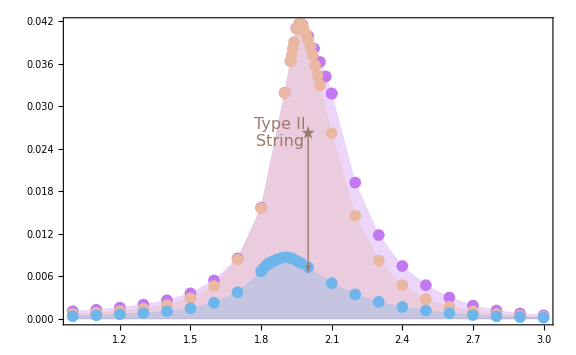

```mathematica
ListLinePlot[Evaluate[points/@{3.5,4.0,4.5}],PlotTheme->"Scientific",PlotMarkers->{"●", 12},PlotStyle->Evaluate[{Thickness[0.00],#}&/@palette],ImageSize->Large,FrameLabel->Evaluate[Style[#,25,FontFamily->"Times New Roman [TMC ]"]&/@{"",""}],FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"],Filling->Bottom,PlotRangePadding->{None,{0,Scaled[0.02]}},PlotRange->{{1,
3},{0,All}},FrameTicksStyle->Directive[20,FontFamily->"Times New Roman [TMC ]"]];
Graphics[{
Darker@palette[[2]],Thick,
Arrowheads[.03],
GeometricTransformation[star,Composition[TranslationTransform[{2,15/572}],ScalingTransform[0.015{2,0.0415GoldenRatio}]]],
Text[Style["Type II\nString",16],{2-0.12,15/572}],
Arrow[{{2,15/572},{2,15/2288}}],
Darker@palette[[1]],
SpecialTextRotation[Style["",18],{2.22,0.025},-1.25,{2,0.0415}],
Darker@palette[[2]],
SpecialTextRotation[Style["",18],{2.2,0.01},-1.0,{2,0.0415}],
Darker@palette[[3]],
SpecialTextRotation[Style["",18],{2.05,0.004},-0.45,{2,0.0415}]
}];
(*ParametricPlot[{2,-(15 (-4+3 ϵ))/2288},{ϵ,0,1},PlotStyle->{Thick,Darker@palette[[2]]}];*)
Show[%%,%]
```

```mathematica
Export[NotebookDirectory[]<>"/Figures/graviton_traj_sara.pdf",]
```

/home/sbr/Physics/Gapped Bootstrap/Code For "The Rise of Linear Trajectories"//Figures/graviton_traj_sara.pdf

### End